## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
?dispersion`*
```

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Prepare Spectrum

```mathematica
dataFakeNoCrossing={{-1,1.3},{-0.8,1.4},{-0.7,1.5},{-0.6,1.7},{-0.5,2},{0,2.5},{0.5,8},{1,6}}
dataFake={{-1,-1.3},{-0.8,-1.0},{-0.7,-0.8},{-0.6,-0.3},{-0.5,-0.1},{0,0.5},{0.5,8},{1,6}}
```

{{-1,1.3},{-0.8,1.4},{-0.7,1.5},{-0.6,1.7},{-0.5,2},{0,2.5},{0.5,8},{1,6}}

{{-1,-1.3},{-0.8,-1.},{-0.7,-0.8},{-0.6,-0.3},{-0.5,-0.1},{0,0.5},{0.5,8},{1,6}}

```mathematica
spectFunCrossing[u_]=CoefficientList[
Fit[dataFake2,{1,u,u^2,u^3,u^4,u^5},u],
u].{1,u,u^2,u^3,u^4,u^5}
```

0.505427+5.64078 u+17.6868 u^2+13.9023 u^3-15.8373 u^4-15.8978 u^5

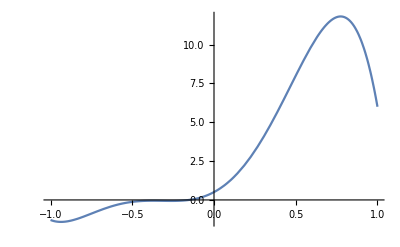

```mathematica
Plot[spectFunCrossing[u],{u,-1,1}]
```

```mathematica
spectFun[u_]=CoefficientList[
Fit[dataFake,{1,u,u^2,u^3,u^4,u^5},u],
u].{1,u,u^2,u^3,u^4,u^5}
```

0.505427+5.64078 u+17.6868 u^2+13.9023 u^3-15.8373 u^4-15.8978 u^5

```mathematica
Plot[spectFun[u],{u,-1,1}]
```

-Graphics-

I can try to find the three useful integrals analytically. It can be done but I will try to do this more generally.

```mathematica
Assuming[n∈Reals,
Integrate[(spectFun@u)/(1-n u),{u,-1,1}]
]
```

ConditionalExpression[1/n^6(n (22.5476+n (23.0437+n (-10.6999+(-17.6554-10.5827 n) n)))+(11.2738+n (11.5219+n (-9.1079+n (-12.6683+(-4.51014-2.50958 n) n)))) Log[1.-1. n]+(-11.2738+n (-11.5219+n (9.1079+n (12.6683+n (4.51014+2.50958 n))))) Log[1.+1. n]),-1.<n<1.]

```mathematica
Assuming[n∈Reals,
Integrate[(spectFun@u)u/(1-n u),{u,-1,1}]
]
```

ConditionalExpression[1/n^7(n (22.5476+n (23.0437+n (-10.6999+n (-17.6554+(-10.5827-8.85595 n) n))))+(11.2738+n (11.5219+n (-9.1079+n (-12.6683+(-4.51014-2.50958 n) n)))) Log[1.-1. n]+(-11.2738+n (-11.5219+n (9.1079+n (12.6683+n (4.51014+2.50958 n))))) Log[1.+1. n]),-1.<n<1.]

```mathematica
Assuming[n∈Reals,
Integrate[(spectFun@u)u^2/(1-n u),{u,-1,1}]
]
```

ConditionalExpression[1/n^8(n (22.5476+n (23.0437+n (-10.6999+n (-17.6554+n (-10.5827+(-8.85595-3.42884 n) n)))))+(11.2738+n (11.5219+n (-9.1079+n (-12.6683+(-4.51014-2.50958 n) n)))) Log[1.-1. n]+(-11.2738+n (-11.5219+n (9.1079+n (12.6683+n (4.51014+2.50958 n))))) Log[1.+1. n]),-1.<n<1.]

Define a test spectrum function which is identity.

```mathematica
spectFun2[u_]:=1
```

Define the three integrals

```mathematica
IntFun0nFF[n_,ct1_,ct2_,spectrumFun_]:= NIntegrate[(spectrumFun@u)/(1-n u),{u,ct1,ct2},Exclusions->{1/n}];
```

```mathematica
IntFun1nFF[n_,ct1_,ct2_,spectrumFun_]:= NIntegrate[(spectrumFun@u)u/(1-n u),{u,ct1,ct2},Exclusions->{1/n}];
```

```mathematica
IntFun2nFF[n_,ct1_,ct2_,spectrumFun_]:= NIntegrate[(spectrumFun@u)u^2/(1-n u),{u,ct1,ct2},Exclusions->{1/n}];
```

```mathematica
IntFun0nFF[0.1,1,-1,spectFun]
IntFun2nFF[0.1,1,-1,spectFun]
IntFun2nFF[1.1,1,1/1.1+0.00001,spectFun]
IntFun2nFF[1.1,1/1.1-0.00001,-1,spectFun]
```

-6.97681

-3.17559

67.2986

-76.4007

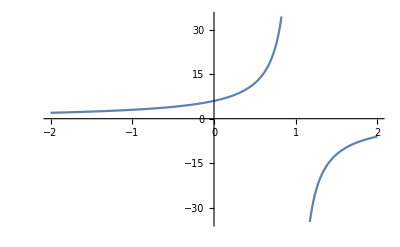

```mathematica
Plot[(spectFun@u)/(1-n u)/.u->1,{n,-2,2},Exclusions->{1}]
```

```mathematica
SpectrumOmegaNMAA[n_?NumberQ,ct1_,ct2_,spectrumFun_]:=(IntFun0nFF[n,ct1,ct2,spectrumFun]-IntFun2nFF[n,ct1,ct2,spectrumFun])/(-4)
```

```mathematica
SpectrumOmegaNMZA[n_?NumberQ,ct1_,ct2_,spectrumFun_]:=-{(IntFun0nFF[n,ct1,ct2,spectrumFun]-IntFun2nFF[n,ct1,ct2,spectrumFun]+√((IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]-2IntFun1nFF[n,ct1,ct2,spectrumFun])(IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]+2IntFun1nFF[n,ct1,ct2,spectrumFun])))/(-4),
(IntFun0nFF[n,ct1,ct2,spectrumFun]-IntFun2nFF[n,ct1,ct2,spectrumFun]-√((IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]-2IntFun1nFF[n,ct1,ct2,spectrumFun])(IntFun0nFF[n,ct1,ct2,spectrumFun]+IntFun2nFF[n,ct1,ct2,spectrumFun]+2IntFun1nFF[n,ct1,ct2,spectrumFun])))/(-4)
}
```

```mathematica
SpectrumOmegaNMAA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.1,1,-1,spectFun]
SpectrumOmegaNMZA[0.9,1,-1,spectFun]
SpectrumOmegaNMZA[0.999,1,-1,spectFun]
SpectrumOmegaNMZA[0.9999,1,-1,spectFun]
```

0.950305

{-0.950305+0.228713 ⅈ,-0.950305-0.228713 ⅈ}

{0.261912,-4.44022}

{1.63945,-7.21879}

{2.24767,-7.86506}

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun2][[1]],
{n,-2,2}
]
```

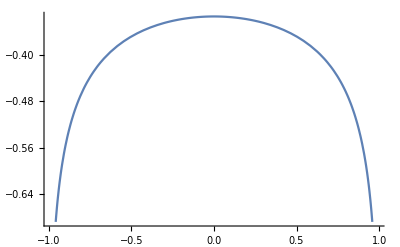

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun2][[1]],
{n,-0.99,0.99}
]
```

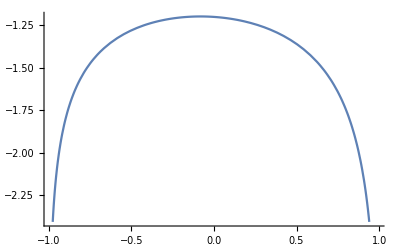

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun][[1]],
{n,-0.99,0.99}
]
```

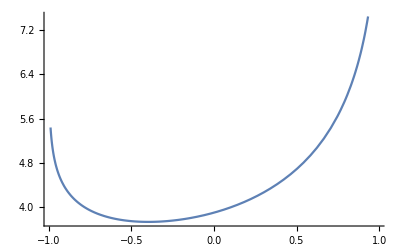

```mathematica
Plot[
SpectrumOmegaNMZA[n,1,-1,spectFun][[2]],
{n,-0.99,0.99}
]
```

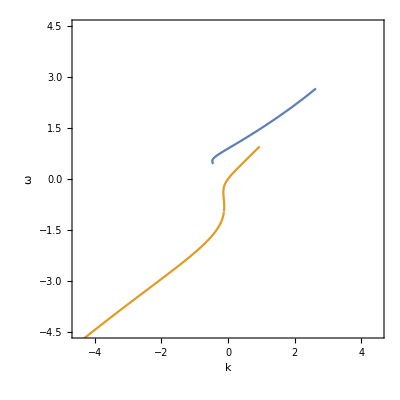

```mathematica
pltSpect=ParametricPlot[
{
{n SpectrumOmegaNMAA[n,1,-1,spectFun],SpectrumOmegaNMAA[n,1,-1,spectFun]},
{n *#,#}&/@SpectrumOmegaNMZA[n,1,-1,spectFun]
},
{n,-0.99,0.99},
PlotRange->{{-4.5,4.5},{-4.5,4.5}},
Frame->True,
FrameLabel->{"k","ω"}
]//Quiet
```

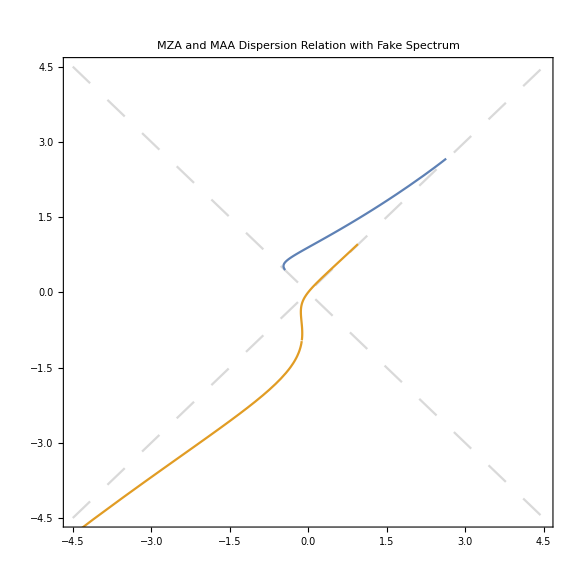

```mathematica
pltSpectGrids=Show[
Plot[{x,-x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLabel->"MZA and MAA Dispersion Relation with Fake Spectrum",AspectRatio->1],
pltSpect
]
```

Linear Stability Analysis

I need to find the unstable values.

### Solve MAA

```mathematica
SpectrumOmegaNMAA[0.3,1,-1,spectFun]
```

1.5035

```mathematica
SpectrumOmegaKMAAEqnLHS[omegaR_?NumberQ,omegaI_?NumericQ,kR_?NumberQ,kI_?NumberQ,spect_]:=Module[{eqnLHSM,spectM,IntFun0nFFM,IntFun1nFFM,IntFun2nFFM},


spectM=spect;

IntFun0nFFM=NIntegrate[(spectM@u)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun2nFFM=NIntegrate[(spectM[u]u^2)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];


eqnLHSM[omega_,k_]:=omega-(IntFun0nFFM-IntFun2nFFM)/(-4);


{ComplexExpand[Re[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]],
ComplexExpand[Im[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]]
}


]
```

```mathematica
SpectrumOmegaKMAAEqnLHS[0.4,0,0.3,0,spectFun]
```

{2.40589,0}

Test FindRoot on this problem

```mathematica
FindRoot[
SpectrumOmegaKMAAEqnLHS[0.4,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
```

{kreal→-107.477,kimag→-2.78188×10^-24}

I need to generate all the results for different real omegas

```mathematica
maalsadata=Table[
{omegareal,
{kreal,kimag}/.FindRoot[
SpectrumOmegaKMAAEqnLHS[omegareal,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
},
{omegareal,-0.91,0.91,0.1}
]
```

{{-0.91,{0.99985,1.11213}},{-0.81,{1.06755,1.26625}},{-0.71,{1.13681,1.39729}},{-0.61,{1.20884,1.51032}},{-0.51,{1.28496,1.60857}},{-0.41,{1.36661,1.69449}},{-0.31,{1.45532,1.77035}},{-0.21,{1.55257,1.83863}},{-0.11,{1.65947,1.90231}},{-0.01,{1.77627,1.96472}},{0.09,{4.01402,-8.93432×10^-18}},{0.19,{6114.29,1.47512×10^-24}},{0.29,{-9331.45,-4.40807×10^-17}},{0.39,{12548.6,8.65899×10^-20}},{0.49,{543.912,-3.52704×10^-21}},{0.59,{-3220.55,8.05514×10^-26}},{0.69,{22200.1,3.31444×10^-26}},{0.79,{25417.3,2.37077×10^-28}},{0.89,{28634.4,9.14921×10^-27}}}

```mathematica
Export["maalsadata.csv",Flatten@#&/@maalsadata]
```

maalsadata.csv

### Solve MZA

```mathematica
SpectrumOmegaKMZApEqnLHS[omegaR_?NumberQ,omegaI_?NumericQ,kR_?NumberQ,kI_?NumberQ,spect_]:=Module[{eqnLHSM,spectM,IntFun0nFFM,IntFun1nFFM,IntFun2nFFM},


spectM=spect;

IntFun0nFFM=NIntegrate[(spectM@u)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun1nFFM=NIntegrate[(spectM@u)u/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun2nFFM=NIntegrate[(spectM[u]u^2)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];


eqnLHSM[omega_,k_]:=omega-(IntFun0nFFM-IntFun2nFFM+√((IntFun0nFFM+IntFun2nFFM-2IntFun1nFFM)(IntFun0nFFM+IntFun2nFFM+2IntFun1nFFM)))/(-4);



{ComplexExpand[Re[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]],
ComplexExpand[Im[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]]
}


]
```

```mathematica
SpectrumOmegaKMZAmEqnLHS[omegaR_?NumberQ,omegaI_?NumericQ,kR_?NumberQ,kI_?NumberQ,spect_]:=Module[{eqnLHSM,spectM,IntFun0nFFM,IntFun1nFFM,IntFun2nFFM},


spectM=spect;

IntFun0nFFM=NIntegrate[(spectM@u)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun1nFFM=NIntegrate[(spectM@u)u/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];
IntFun2nFFM=NIntegrate[(spectM[u]u^2)/(1-(kR+I*kI) u/(omegaR+I*omegaI)),{u,-1,1}];


eqnLHSM[omega_,k_]:=omega-(IntFun0nFFM-IntFun2nFFM-√((IntFun0nFFM+IntFun2nFFM-2IntFun1nFFM)(IntFun0nFFM+IntFun2nFFM+2IntFun1nFFM)))/(-4);



{ComplexExpand[Re[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]],
ComplexExpand[Im[
eqnLHSM[omegaR+I omegaI,kR+I kI]
]]
}


]
```

```mathematica
FindRoot[
SpectrumOmegaKMZApEqnLHS[0.3,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
```

{kreal→-6.14831,kimag→-0.0152747}

```mathematica
FindRoot[
SpectrumOmegaKMZAmEqnLHS[0.3,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]//Quiet
```

{kreal→-209.741,kimag→-0.0319845}

```mathematica
mzaplsadata=Table[
{omegareal,
{kreal,kimag}/.FindRoot[
SpectrumOmegaKMZApEqnLHS[omegareal,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
},
{omegareal,-4.491,4.491,0.5}
]//Quiet
```

{{-4.491,{-1.87435,-6.31089×10^-30}},{-3.991,{-0.364055,-3.13777×10^-26}},{-3.491,{1.60332,1.70751}},{-2.991,{1.8415,2.93876}},{-2.491,{2.08266,3.75327}},{-1.991,{2.33021,4.37731}},{-1.491,{2.59125,4.87178}},{-0.991,{2.87742,5.26145}},{-0.491,{3.20731,5.55987}},{0.009,{9.64253,4.64449}},{0.509,{-3141.52,-0.0937844}},{1.009,{-283732.,3.36774×10^-7}},{1.509,{-1751.42,0.0000306366}},{2.009,{-426878.,-0.0000112193}},{2.509,{-326157.,429660.}},{3.009,{-442116.,0.000111045}},{3.509,{-47542.4,0.379289}},{4.009,{47643.7,-24791.9}}}

```mathematica
Export["mzaplsadata.csv",Flatten@#&/@mzaplsadata]
```

mzaplsadata.csv

```mathematica
mzamlsadata=Table[
{omegareal,
{kreal,kimag}/.FindRoot[
SpectrumOmegaKMZAmEqnLHS[omegareal,0,kreal,kimag,spectFun],
{kreal,0.1},{kimag,0.1}
]
},
{omegareal,-4.491,4.491,0.5}
]//Quiet
```

{{-4.491,{95.2511,-1.46433×10^-8}},{-3.991,{95.5903,-5.42315×10^-11}},{-3.491,{69599.1,-0.0163735}},{-2.991,{61155.7,-0.00152951}},{-2.491,{9974.9,0.00244043}},{-1.991,{1239.94,0.0377071}},{-1.491,{261262.,-8.46935×10^-9}},{-0.991,{-14220.3,176316.}},{-0.491,{-7014.36,41106.6}},{0.009,{-0.0266733,1.83325}},{0.509,{-0.0979696,1.48075}},{1.009,{-0.103901,0.814719}},{1.509,{0.998335,-3.96403×10^-29}},{2.009,{1.76647,-8.27515×10^-28}},{2.509,{2.38374,-3.80146×10^-23}},{3.009,{2.94442,-2.12644×10^-16}},{3.509,{3.47677,-5.54715×10^-20}},{4.009,{3.99369,-5.34643×10^-24}}}

```mathematica
Export["mzamlsadata.csv",Flatten@#&/@mzamlsadata]
```

mzamlsadata.csv

### Generate Map

```mathematica
maalsadata=Import["maalsadata-crossing-supernova.csv"];
mzaplsadata=Import["mzaplsadata-crossing-supernova.csv"];
mzamlsadata=Import["mzamlsadata-crossing-supernova.csv"];
```

```mathematica
Flatten@#&/@maalsadata
```

```mathematica
maalsadataClean=Select[Flatten@#&/@maalsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
mzaplsadataClean=Select[Flatten@#&/@mzaplsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
mzamlsadataClean=Select[Flatten@#&/@mzamlsadata,(-4.5<#[[1]]<4.5)&&(-4.5<#[[2]]<4.5)&&(-500<#[[3]]<500)&];
```

```mathematica
mzamlsadataClean
mzaplsadataClean
```

```mathematica
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@maalsadataClean//Quiet
```

$Aborted

```mathematica
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@{Last@maalsadataClean}
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0234064}. NIntegrate obtained -0.441553 - 1.2808×10^-16\ ⅈ and 0.278924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {0.0234064}. NIntegrate obtained -0.0815534 - 2.56311×10^-19\ ⅈ and 0.00014022 for the integral and error estimates.

{{3.15026×10^-15,-3.19559×10^-17}}

```mathematica
Part[maalsadataClean,
Flatten@Position[
Chop[
SpectrumOmegaKMAAEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@(Flatten@#&/@maalsadataClean),
10^(-5)
]//Quiet,
{0,0}]
];
```

```mathematica
Show[
Graphics[
{Point[-{#[[2]],#[[1]]}&/@maalsadataClean,VertexColors->colorf/@Rescale@(#[[3]]&/@maalsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@maalsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MAA",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
],FrameLabel->{"omega","k"}
]
```

-Graphics-

```mathematica
mzaplsadataClean
```

{{-2.191,-4.48891,-4.56117},{-2.091,-4.36108,4.63206},{-1.991,-4.23356,4.70304},{-1.891,-4.10637,4.77405},{-0.191,-1.94626,5.88681},{-0.091,-1.81083,5.94072}}

```mathematica
Part[mzaplsadata,
Flatten@Position[
Chop[
SpectrumOmegaKMZApEqnLHS[#[[1]],0,#[[2]],#[[3]],spectFun]&/@(Flatten@#&/@mzaplsadata),
10^(-5)
]//Quiet,
{0,0}]
]
```

{{-4.491,-4.06179,-4.2042×10^-18},{-4.481,-4.04889,3.13562×10^-19},{-4.471,-4.03598,3.39165×10^-19},{-4.461,-4.02306,1.25008×10^-19},{-4.451,-4.01014,3.44643×10^-20},{-4.441,-3.99721,8.1013×10^-21},{-4.431,-3.98427,1.61881×10^-21},{-4.421,-3.97132,2.93423×10^-22},{-4.411,-3.95836,4.70475×10^-23},{-4.401,-3.9454,2.177×10^-24},{-4.391,-3.93243,5.3274×10^-25},{-4.381,-3.91945,-1.44999×10^-25},{-4.371,-3.90646,-2.28202×10^-26},{-4.361,-3.89347,3.03932×10^-26},{-4.351,-3.88046,-9.16341×10^-27},{-4.341,-3.86745,4.31665×10^-27},{-4.331,-3.85443,-1.22431×10^-27},{-4.321,-3.84141,6.24778×10^-28},{-4.311,-3.82837,7.57306×10^-29},{-4.301,-3.81533,-3.78653×10^-29},{-4.291,-3.80228,1.30905×10^-15},{-4.281,-3.78923,-4.73317×10^-30},{-4.271,-3.77616,2.40677×10^-16},{-4.261,-3.76309,9.96558×10^-17},{-4.251,-3.75001,4.00908×10^-17},{-4.241,-3.73692,1.55773×10^-17},{-4.231,-3.72383,5.78738×10^-18},{-4.221,-3.71073,2.02684×10^-18},{-4.211,-3.69762,6.76838×10^-19},{-4.201,-3.6845,2.04875×10^-19},{-4.191,-3.67138,5.31519×10^-20},{-4.181,-3.65825,1.01581×10^-20},{-4.171,-3.64511,2.72621×10^-23},{-4.161,-3.63197,-1.19845×10^-21},{-4.151,-3.61882,-8.15768×10^-22},{-4.141,-3.60566,-4.13164×10^-22},{-4.131,-3.59249,-2.59085×10^-21},{-4.121,-3.57932,-1.25557×10^-21},{-4.111,-3.56614,3.21502×10^-24},{-4.101,-3.55296,2.09849×10^-23},{-4.091,-3.53976,-6.62138×10^-26},{-4.081,-3.52656,-2.79295×10^-25},{-4.071,-3.51336,6.24525×10^-26},{-4.061,-3.50014,2.58115×10^-27},{-4.051,-3.48692,-1.73549×10^-29},{-4.041,-3.4737,8.83524×10^-29},{-4.031,-3.46046,5.91646×10^-29},{-4.021,-3.44722,-1.82424×10^-30},{-4.011,-3.43398,-6.90253×10^-30},{-4.001,-3.42072,-2.42667×10^-16},{-3.991,-3.40747,-9.24446×10^-32},{-3.981,-3.3942,4.01793×10^-17},{-3.971,-3.38093,1.27605×10^-17},{-3.961,-3.36765,-1.83951×10^-18},{-3.951,-3.35437,-2.62228×10^-18},{-3.941,-3.34108,-5.43656×10^-19},{-3.931,-3.32778,2.47488×10^-19},{-3.921,-3.31448,1.65235×10^-19},{-3.911,-3.30117,8.62529×10^-21},{-3.901,-3.28786,-2.54339×10^-20},{-3.891,-3.27454,-8.73099×10^-21},{-3.881,-3.26121,1.92407×10^-21},{-3.871,-3.24788,2.27497×10^-21},{-3.861,-3.23455,3.5946×10^-22},{-3.851,-3.2212,-3.42393×10^-22},{-3.841,-3.20786,-1.83098×10^-22},{-3.831,-3.1945,8.75325×10^-24},{-3.821,-3.18114,4.71913×10^-23},{-3.811,-3.16778,1.4514×10^-23},{-3.801,-3.15441,-6.38682×10^-24},{-3.791,-3.14103,-4.98934×10^-24},{-3.781,-3.12765,-2.11561×10^-24},{-3.771,-3.11427,1.25693×10^-24},{-3.761,-3.10088,7.62052×10^-25},{-3.751,-3.08748,4.7319×10^-26},{-3.741,-3.07408,-3.27914×10^-25},{-3.731,-3.06068,-1.98111×10^-25},{-3.721,-3.04727,5.63941×10^-26},{-3.711,-3.03386,3.35739×10^-26},{-3.701,-3.02044,1.67617×10^-26},{-3.691,-3.00701,1.79781×10^-27},{-3.681,-2.99359,-1.19907×10^-26},{-3.671,-2.98015,-5.30115×10^-27},{-3.661,-2.96672,1.03499×10^-27},{-3.651,-2.95328,1.3884×10^-28},{-3.641,-2.93983,6.65168×10^-27},{-3.631,-2.92638,1.07601×10^-27},{-3.621,-2.91293,-5.0566×10^-28},{-3.611,-2.89947,-2.8399×10^-27},{-3.601,-2.88601,6.31089×10^-28},{-3.591,-2.87254,6.56332×10^-28},{-3.581,-2.85908,-1.07285×10^-28},{-3.571,-2.8456,5.74291×10^-28},{-3.561,-2.83213,7.22597×10^-28},{-3.551,-2.81865,1.64083×10^-28},{-3.541,-2.80517,-2.32714×10^-29},{-3.531,-2.79168,-4.85938×10^-28},{-3.521,-2.77819,1.10441×10^-29},{-3.511,-2.7647,-4.52806×10^-28},{-3.501,-2.75121,-6.68954×10^-28},{-3.491,-2.73771,-2.42969×10^-28},{-3.481,-2.72421,2.8399×10^-29},{-3.471,-2.71071,1.0413×10^-28},{-3.461,-2.6972,4.81205×10^-29},{-3.451,-2.68369,3.15544×10^-29},{-3.441,-2.67018,5.59942×10^-16},{-3.431,-2.65667,-1.0678×10^-15},{-3.421,-2.64316,1.38051×10^-29},{-3.411,-2.62964,-2.76101×10^-29},{-3.401,-2.61612,-5.48258×10^-29},{-3.391,-2.6026,1.61716×10^-29},{-3.381,-2.58908,-3.24311×10^-15},{-3.371,-2.57555,-6.31089×10^-30},{-3.361,-2.56203,7.09975×10^-30},{-3.351,-2.5485,1.57772×10^-29},{-3.341,-2.53498,3.27377×10^-29},{-3.331,-2.52145,-1.75522×10^-29},{-3.321,-2.50792,-8.50081×10^-16},{-3.311,-2.49439,3.74709×10^-30},{-3.301,-2.48086,1.18329×10^-30},{-3.291,-2.46732,8.38165×10^-31},{-3.281,-2.45379,6.66473×10^-18},{-3.271,-2.44026,9.75581×10^-17},{-3.261,-2.42673,1.51293×10^-16},{-3.251,-2.4132,1.78315×10^-16},{-3.241,-2.39966,-8.13513×10^-31},{-3.231,-2.38613,1.06003×10^-30},{-3.221,-2.3726,1.63283×10^-16},{-3.211,-2.35907,1.44435×10^-16},{-3.201,-2.34554,1.21877×10^-16},{-3.191,-2.33201,1.01711×10^-16},{-3.181,-2.31848,8.23276×10^-17},{-3.171,-2.30495,6.47785×10^-17},{-3.161,-2.29143,5.00679×10^-17},{-3.151,-2.27791,3.81313×10^-17},{-3.141,-2.26438,2.81612×10^-17},{-3.131,-2.25086,2.07134×10^-17},{-3.121,-2.23734,1.48179×10^-17},{-3.111,-2.22383,1.04038×10^-17},{-3.101,-2.21031,7.14797×10^-18},{-3.091,-2.1968,4.82309×10^-18},{-3.081,-2.1833,3.16341×10^-18},{-3.071,-2.16979,2.08947×10^-18},{-3.061,-2.15629,1.31931×10^-18},{-3.051,-2.14279,8.12056×10^-19},{-3.041,-2.12929,4.82064×10^-19},{-3.031,-2.1158,2.84103×10^-19},{-3.021,-2.10232,1.61546×10^-19},{-3.011,-2.08883,8.72271×10^-20},{-3.001,-2.07535,4.53972×10^-20},{-2.991,-2.06188,2.1656×10^-20},{-2.981,-2.04841,9.33559×10^-21},{-2.971,-2.03494,3.27151×10^-21},{-2.961,-2.02149,5.1434×10^-22},{-2.951,-2.00803,-5.24731×10^-22},{-2.941,-1.99458,-7.28597×10^-22},{-2.931,-1.98114,-7.0338×10^-22},{-2.921,-1.96771,-5.26943×10^-22},{-2.911,-1.95428,-3.53277×10^-22},{-2.901,-1.94085,-2.23705×10^-22},{-2.891,-1.92744,-1.31674×10^-22},{-2.881,-1.91403,-8.03496×10^-23},{-2.871,-1.90063,-4.02475×10^-23},{-2.861,-1.88723,-2.13262×10^-23},{-2.851,-1.87385,-1.04561×10^-23},{-2.841,-1.86047,-5.4104×10^-24},{-2.831,-1.8471,-2.54798×10^-24},{-2.821,-1.83374,-1.07093×10^-24},{-2.811,-1.82039,-7.87498×10^-25},{-2.801,-1.80705,-3.42807×10^-25},{-2.791,-1.79372,-1.7832×10^-25},{-2.781,-1.7804,-7.09344×10^-26},{-2.771,-1.76709,-2.00434×10^-26},{-2.761,-1.75379,-1.60044×10^-26},{-2.751,-1.7405,-1.18014×10^-27},{-2.741,-1.72722,-5.64824×10^-28},{-2.731,-1.71395,-5.09604×10^-28},{-2.721,-1.70069,4.73317×10^-30},{-2.711,-1.68745,1.22273×10^-28},{-2.701,-1.67422,-2.76101×10^-29},{-2.691,-1.661,-1.04524×10^-29},{-2.681,-1.6478,8.87469×10^-31},{-2.671,-1.63461,3.59918×10^-30},{-2.661,-1.62143,1.45996×10^-16},{-2.651,-1.60827,6.74567×10^-17},{-2.641,-1.59512,2.95472×10^-17},{-2.631,-1.58199,1.76705×10^-28},{-2.621,-1.56887,-9.70299×10^-29},{-2.611,-1.55577,4.06263×10^-29},{-2.601,-1.54269,-7.82955×10^-16},{-2.591,-1.52962,-2.22254×10^-16},{-2.581,-1.51657,-4.03769×10^-17},{-2.571,-1.50353,7.73022×10^-18},{-2.561,-1.49052,1.41909×10^-17},{-2.551,-1.47752,1.05633×10^-17},{-2.541,-1.46454,6.31648×10^-18},{-2.531,-1.45158,3.36429×10^-18},{-2.521,-1.43864,1.67382×10^-18},{-2.511,-1.42573,7.85931×10^-19},{-2.501,-1.41283,3.55127×10^-19},{-2.491,-1.39995,1.57842×10^-19},{-2.481,-1.38709,6.58398×10^-20},{-2.471,-1.37426,2.72369×10^-20},{-2.461,-1.36145,1.0804×10^-20},{-2.451,-1.34866,4.34673×10^-21},{-2.441,-1.3359,1.6884×10^-21},{-2.431,-1.32316,6.22861×10^-22},{-2.421,-1.31044,2.27849×10^-22},{-2.411,-1.29775,8.44774×10^-23},{-2.401,-1.28509,3.03197×10^-23},{-2.391,-1.27245,1.21331×10^-23},{-2.381,-1.25984,4.13469×10^-24},{-2.371,-1.24725,1.02953×10^-24},{-2.361,-1.2347,3.58054×10^-25},{-2.351,-1.22217,1.35406×10^-25},{-2.341,-1.20967,-1.47422×10^-26},{-2.331,-1.19721,-1.1713×10^-26},{-2.321,-1.18477,2.24668×10^-27},{-2.311,-1.17236,-1.02236×10^-27},{-2.301,-1.15999,-2.05735×10^-27},{-2.291,-1.14764,-6.05845×10^-28},{-2.281,-1.13533,5.6798×10^-29},{-2.271,-1.12306,1.2464×10^-28},{-2.261,-1.11081,5.52203×10^-30},{-2.251,-1.09861,-2.2877×10^-29},{-2.241,-1.08644,1.59836×10^-15},{-2.231,-1.0743,8.67887×10^-16},{-2.221,-1.0622,4.64824×10^-16},{-2.211,-1.05014,2.47794×10^-16},{-2.201,-1.03812,2.21867×10^-31},{-2.191,-1.02614,6.77181×10^-17},{-2.181,-1.01419,3.49704×10^-17},{-2.171,-1.00229,1.77927×10^-17},{-2.161,-0.990429,8.9482×10^-18},{-2.151,-0.97861,4.42984×10^-18},{-2.141,-0.966833,2.21356×10^-18},{-2.131,-0.955101,1.05293×10^-18},{-2.121,-0.943413,5.20111×10^-19},{-2.111,-0.931771,2.37946×10^-19},{-2.101,-0.920174,1.13302×10^-19},{-2.091,-0.908625,4.93535×10^-20},{-2.081,-0.897123,2.25325×10^-20},{-2.071,-0.88567,1.01211×10^-20},{-2.061,-0.874266,4.58589×10^-21},{-2.051,-0.862912,1.87156×10^-21},{-2.041,-0.85161,7.047×10^-22},{-2.031,-0.84036,2.94438×10^-22},{-2.021,-0.829162,1.3464×10^-22},{-2.011,-0.818019,3.90649×10^-23},{-2.001,-0.80693,1.3663×10^-23},{-1.991,-0.795897,1.00166×10^-25},{-1.981,-0.78492,3.8976×10^-25},{-1.971,-0.774001,1.36618×10^-25},{-1.961,-0.76314,-6.61381×10^-27},{-1.951,-0.752338,5.49047×10^-28},{-1.941,-0.741597,3.15544×10^-29},{-1.931,-0.730916,2.05104×10^-29},{-1.921,-0.720298,8.62817×10^-32},{-1.911,-0.709743,-8.62817×10^-32},{-1.901,-0.699252,2.67517×10^-17},{-1.891,-0.688826,4.62223×10^-33},{-1.881,-0.678466,1.43118×10^-18},{-1.871,-0.668174,2.16854×10^-20},{-1.861,-0.657949,-1.03971×10^-19},{-1.851,-0.647793,-1.75615×10^-20},{-1.841,-0.637707,-4.12246×10^-22},{-1.831,-0.627692,2.07933×10^-22},{-1.821,-0.617749,8.83108×10^-21},{-1.811,-0.607879,2.91902×10^-20},{-1.801,-0.598083,6.63761×10^-20},{-1.791,-0.588361,1.08255×10^-19},{-1.781,-0.578716,1.46412×10^-19},{-1.771,-0.569148,1.96292×10^-19},{-1.761,-0.559658,2.51211×10^-19},{-1.751,-0.550247,3.22639×10^-19},{-1.741,-0.540916,4.16114×10^-19},{-1.731,-0.531666,5.52031×10^-19},{-1.721,-0.522498,7.27061×10^-19},{-1.711,-0.513413,9.40683×10^-19},{-1.701,-0.504413,1.16635×10^-18},{-1.691,-0.495497,1.4427×10^-18},{-1.681,-0.486667,1.7093×10^-18},{-1.671,-0.477925,1.94932×10^-18},{-1.661,-0.46927,2.17261×10^-18},{-1.651,-0.460704,2.32368×10^-18},{-1.641,-0.452229,2.45339×10^-18},{-1.631,-0.443844,2.48347×10^-18},{-1.621,-0.435551,2.39673×10^-18},{-1.611,-0.42735,2.32906×10^-18},{-1.601,-0.419244,2.03271×10^-18},{-1.591,-0.411232,1.76518×10^-18},{-1.581,-0.403316,1.45115×10^-18},{-1.571,-0.395496,1.07979×10^-18},{-1.561,-0.387773,6.82647×10^-19},{-1.551,-0.380149,3.27786×10^-19},{-1.541,-0.372624,-3.24805×10^-20},{-1.531,-0.365198,-3.00123×10^-19},{-1.521,-0.357873,-5.90471×10^-19},{-1.511,-0.35065,-8.1412×10^-19},{-1.501,-0.343529,-9.93915×10^-19},{-1.491,-0.33651,-1.13202×10^-18},{-1.481,-0.329596,-1.21065×10^-18},{-1.471,-0.322786,-1.25239×10^-18},{-1.461,-0.316081,-1.26865×10^-18},{-1.451,-0.309482,-1.23485×10^-18},{-1.441,-0.30299,-1.19848×10^-18},{-1.431,-0.296604,-1.14773×10^-18},{-1.421,-0.290326,-1.02237×10^-18},{-1.411,-0.284157,-8.5222×10^-19},{-1.401,-0.278096,-6.21855×10^-19},{-1.391,-0.272145,-2.52416×10^-19},{-1.381,-0.266303,2.90276×10^-19},{-1.371,-0.260572,1.00482×10^-18},{-1.361,-0.254951,1.95389×10^-18},{-1.351,-0.249441,2.94499×10^-18},{-1.341,-0.244043,3.39057×10^-18},{-1.331,-0.238757,1.69667×10^-18},{-1.321,-0.233583,-5.32115×10^-18},{-1.311,-0.228521,-2.10397×10^-17},{-1.301,-0.223572,-3.44071×10^-17},{-1.291,-0.218735,-2.36728×10^-20},{-1.281,-0.214011,-4.31962×10^-20},{-1.271,-0.209401,-6.91416×10^-20},{-1.261,-0.204903,-8.41901×10^-20},{-1.251,-0.200519,-4.43131×10^-21},{-1.241,-0.196248,4.68006×10^-19},{-1.231,-0.19209,2.11339×10^-18},{-1.221,-0.188046,6.45347×10^-18},{-1.211,-0.184114,1.32389×10^-17},{-1.201,-0.180295,4.4839×10^-19},{-1.191,-0.176589,-1.70955×10^-16},{-1.181,-0.172995,-1.01115×10^-15},{-1.171,-0.169514,6.48444×10^-28},{-1.161,-0.166144,-1.72445×10^-26},{-1.151,-0.162886,-5.78885×10^-25},{-1.141,-0.159739,1.71506×10^-22},{-1.131,-0.156703,1.54909×10^-20},{-1.121,-0.153777,-1.48604×10^-17},{-1.111,-0.15096,2.91247×10^-27},{-1.101,-0.148253,-1.83004×10^-19},{-1.091,-0.145654,3.12428×10^-23},{-1.081,-0.143163,9.02329×10^-20},{-1.071,-0.14078,-5.11856×10^-16},{-1.061,-0.138503,4.71908×10^-21},{-1.051,-0.136331,-1.03688×10^-26},{-1.041,-0.134264,-2.11386×10^-15},{-1.031,-0.132302,1.29437×10^-22},{-1.021,-0.130442,-4.83118×10^-19},{-1.011,-0.128684,1.42448×10^-18},{-1.001,-0.127028,-7.82799×10^-18},{-0.991,-0.125471,-8.18299×10^-23},{-0.981,-0.124014,1.8301×10^-15},{-0.971,-0.122654,4.31588×10^-15},{-0.211,-1.25017,-2.55777×10^-17},{-0.201,-1.26699,3.29609×10^-19},{-0.191,-1.34554,-4.39026×10^-20},{-0.181,-1.18509,1.2344×10^-19},{-0.171,-1.22941,-3.24648×10^-17},{-0.161,-1.20868,-9.60756×10^-18},{-0.151,-1.21034,4.46188×10^-14},{-0.141,-1.21929,1.26463×10^-18},{-0.131,5.62002,0.748908},{-0.121,5.63711,-0.763196},{-0.111,6.46711,-2.13067×10^-17},{-0.101,5.67118,0.7918},{-0.091,5.68816,0.806115},{-0.081,5.70511,0.820436},{-0.071,5.72203,0.834764},{-0.061,5.73891,0.849099},{-0.051,5.75576,0.863438},{-0.041,5.77258,0.877784},{-0.031,5.78931,0.892286},{-0.021,5.80606,0.90671},{-0.011,5.72868,0.942993},{-0.001,5.17827,1.48456},{0.879,-3.60038,1.20282×10^-16},{0.919,-3.84903,6.581×10^-19},{0.949,-4.03355,-8.34352×10^-23},{0.959,-4.18663,-5.19694×10^-19},{0.969,-4.45838,-2.18564×10^-20},{0.989,-4.30021,1.7084×10^-21},{1.009,-4.43586,3.26595×10^-20},{1.019,-4.54781,-1.3647×10^-21},{1.029,-4.80969,-3.54075×10^-26},{1.039,-4.64756,2.20622×10^-25},{1.139,-5.03798,3.2738×10^-24},{1.149,-5.29987,1.37907×10^-19},{1.169,-5.06171,1.25388×10^-23},{1.179,-5.46476,1.75725×10^-25},{1.189,-5.40067,9.79764×10^-23},{1.229,-5.37817,-5.1733×10^-27},{1.239,-6.57637,-4.5636×10^-15},{1.249,-6.09034,1.01035×10^-25},{1.259,-5.60527,-2.81129×10^-24},{1.309,-6.23224,8.38028×10^-30},{1.329,-6.60627,1.1272×10^-14},{1.339,-6.23153,-1.67698×10^-15},{1.369,-6.47532,-9.96205×10^-35},{1.379,-6.59855,-2.48539×10^-40},{1.399,-6.7118,7.58409×10^-15},{1.449,-6.78887,-8.9291×10^-15},{1.459,-6.69729,-5.39168×10^-15},{4.099,-7.53671,4.34671×10^-25}}

```mathematica
Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@mzaplsadataClean,VertexColors->colorf/@Rescale@(Abs[#[[3]]]&/@mzaplsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@mzaplsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA+",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
]
]
```

-Graphics-

```mathematica
mzamlsadataClean
```

{}

```mathematica
Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@mzamlsadataClean,VertexColors->colorf/@Rescale@(#[[3]]&/@mzamlsadataClean)],Inset[plotLegend[{Min@#,Max@#}&@(#[[3]]&/@mzamlsadataClean),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega"},PlotLabel->"k.imag for different omega vs k.real: MZA-",
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
Show[
pltSpectGrids
]
]
```

-Graphics-

## Absolute Value of Log Argument

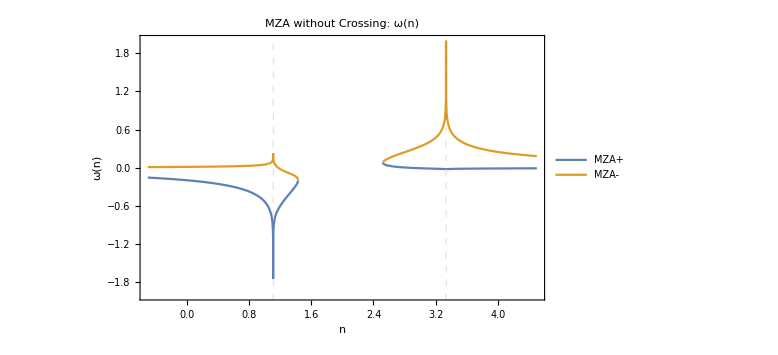

```mathematica
Plot[{ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[2]]},{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{Automatic,{-2,2}},PlotLabel->"MZA without Crossing: ω(n)",FrameLabel->{"n","ω(n)"},Exclusions->{1/0.9,1/0.3},PlotLegends->Placed[{"MZA+","MZA-"},{Right,Top}]]
```

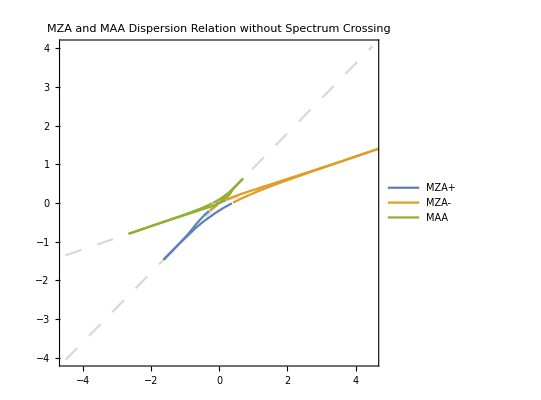

```mathematica
Show[
Plot[{0.3x,0.9x},{x,-4.5,4.5},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,PlotLabel->"MZA and MAA Dispersion Relation without Spectrum Crossing",AspectRatio->1],

ParametricPlot[
{
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[1]]},
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[2]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.3},1}}][[2]]},
{n ConAxialSymOmegaNMAAABS[n,{{{0.9,0.3},1}}],ConAxialSymOmegaNMAAABS[n,{{{0.9,0.3},1}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation without Spectrum Crossing",Exclusions->{1/0.3,1/0.9,1/0.6}]
]
```

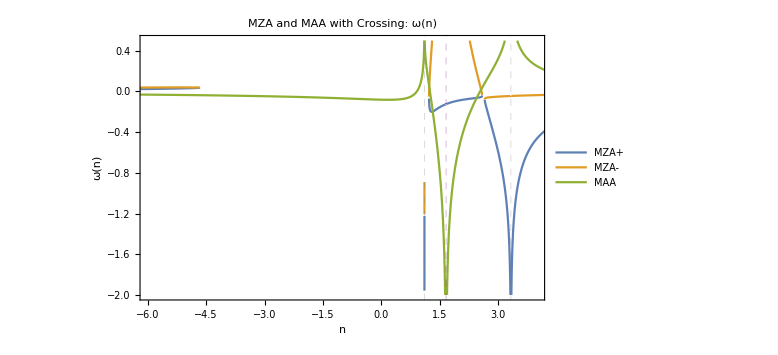

```mathematica
Plot[{ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],
ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMAAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{-6,4},{-2,0.5}},PlotLabel->"MZA and MAA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
```

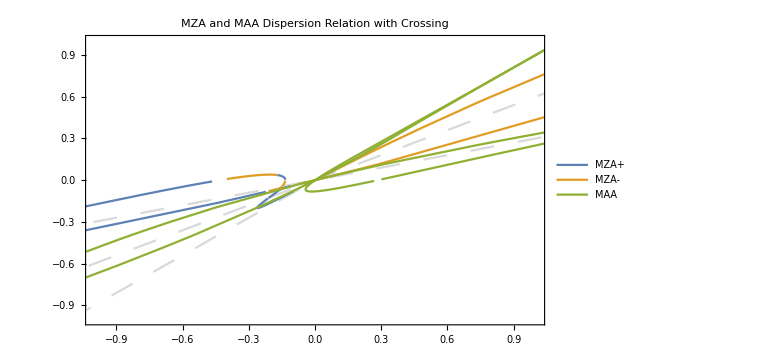

```mathematica
Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-1,1},{-1,1}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},
{n ConAxialSymOmegaNMAAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}],ConAxialSymOmegaNMAAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9,1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

]
```

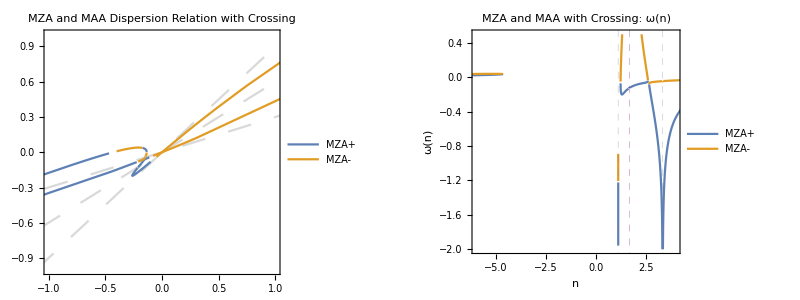

```mathematica
{{Show[Plot[{0.9x,0.6x,0.3x},{x,-7,7},PlotStyle->Directive[LightGray,Dashing[0.03]],Frame->True,ImageSize->Large,PlotRange->{{-1,1},{-1,1}},PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
ParametricPlot[
{
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]]},
{n ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]],ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-2.5,2.5},{-2.5,2.5}},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing",Exclusions->{1/0.9,1/0.6,1/0.3}],
ImagePadding->{{20, 20}, {20, 20}}

],

Plot[{ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[1]],
ConAxialSymOmegaNMZAABS[n,{{{0.9,0.6},3},{{0.6,0.3},-3}}][[2]]},{n,-7,7},Frame->True,ImageSize->Large,GridLines->{{{1/0.3,Directive[Gray,Dashed]},{1/0.6,Directive[Purple,Dashed]},{1/0.9,Directive[Gray,Dashed]}}, None},PlotRange->{{-6,4},{-2,0.5}},PlotLabel->"MZA and MAA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"},PlotLegends->Placed[{"MZA+","MZA-","MAA"},{Right,Top}],Exclusions->{1/0.9,1/0.3,1/0.6}]
}}//Grid
```